## Fig. S6 and S7

Generates all plots for S6 and S7 if run twice: once with oligoStatus=”oligo” and once with oligoStatus=”noOligo”.

```mathematica
Clear["Global`*"]; 
SetDirectory[NotebookDirectory[]];
$MinPrecision=30;
```

```mathematica
oligoStatus="oligo";
```

## specify dynamics

```mathematica
connectedC[σ_]:=Block[{myNeighbors,vars},
(*given a species, find its location in the spatial structure and return sum of connected Subscript[c, σi]*)

myNeighbors=v[[σ]];
vars=ToExpression[Table["c"<>IntegerString[myNeighbors[[a]]],{a,Length[myNeighbors]}]];
Total[vars]

]
```

```mathematica
getCi[n_,nutrientIndex_]:=Block[{k,thisSupply,cVars,cSols,cSystem},

thisSupply=s[[nutrientIndex]];
(*index corresponds to species*)
cVars=ToExpression[Table["c"<>IntegerString[k],{k,Length[n]}]];
cSystem=Table[cVars[[k]]==(thisSupply*n[[k]]+d*connectedC[k])/(α[[k,nutrientIndex]]*n[[k]]+d*z),{k,Length[n]}];
cSols=NSolve[cSystem,cVars]//Flatten;

cVars/.cSols
]
```

```mathematica
dn[n_?(VectorQ[#, NumericQ]&)]:=Block[{(*nutrientIndex,cMatrix,growth*)},

(*matrix of nutrient concentrations. Each row is a nutrient, each column a species: p rows by m columns*)
cMatrix=Table[getCi[n,nutrientIndex],{nutrientIndex,p}];

(*for each species, sum over your column of the cMatrix*)
growth=Table[n[[sigma]]*Total[Table[α[[sigma,nutrientIndex]]*cMatrix[[nutrientIndex,sigma]],{nutrientIndex,p}]]-δ*n[[sigma]],{sigma,Length[n]}]
]
```

## full spatial model, 1D

```mathematica
getPositions[pop0_]:=
Block[{m0,list,extendedPop},
m0=Length[pop0];
extendedPop=Join[{0},pop0];
Table[{Total[extendedPop[[1;;i-1]]],Total[extendedPop[[1;;i]]]},{i,2,m0+1}]
];

getConcentration[n_,nutrient_]:=
Block[{i,m0,c,dc,m,cSys,cSysWrap,cSystem,dcSys,dcSysWrap,dcSystem,totalcSys,vars,aVars,bVars,z},
m0=Length[n];
aVars=ToExpression[Table["a"<>IntegerString[k],{k,m0}]];
bVars=ToExpression[Table["b"<>IntegerString[k],{k,m0}]];
c[a_,b_,α_,θ_]:=a*E^(Sqrt[α/d]*θ)+b*E^(-Sqrt[α/d]*θ)+s[[nutrient]]/α;
dc[a_,b_,α_,θ_]:=Sqrt[α/d]*(a*E^(Sqrt[α/d]*θ)-b*E^(-Sqrt[α/d]*θ));

(*  Create a system of eqs for c(θ) in each region *)
cSys=Table[c[aVars[[i]],bVars[[i]],α[[i,nutrient]],n[[i]]]==c[aVars[[i+1]],bVars[[i+1]],α[[i+1,nutrient]],0],{i,m0-1}];
cSysWrap=c[aVars[[m0]],bVars[[m0]],α[[m0,nutrient]],n[[m0]]]==c[aVars[[1]],bVars[[1]],α[[1,nutrient]],0];
cSystem=Join[cSys,{cSysWrap}];

(*do the same thing for the derivatives of c(θ)*)
dcSys=Table[dc[aVars[[i]],bVars[[i]],α[[i,nutrient]],n[[i]]]==dc[aVars[[i+1]],bVars[[i+1]],α[[i+1,nutrient]],0],{i,m0-1}];
dcSysWrap=dc[aVars[[m0]],bVars[[m0]],α[[m0,nutrient]],n[[m0]]]==dc[aVars[[1]],bVars[[1]],α[[1,nutrient]],0];
dcSystem=Join[dcSys,{dcSysWrap}];

totalcSys=Join[cSystem,dcSystem];
vars=Table[{aVars[[i]],bVars[[i]]},{i,m0}]//Flatten;
{z,m}=CoefficientArrays[totalcSys,vars];
LinearSolve[m,-z]  
];
(*returns {a1,b1,a2,b2...}: in a region σ c_i=a*E^(a*θ/d)+b*E^(-a*θ/d)+si/αi. *)
```

### Dynamics

```mathematica
getGrowth[pop_,species_,c_]:=
Block[{growth,myN,myA,myB},
myN=pop[[species]];
myA=c[[species*2-1]];
myB=c[[species*2]];

growth=Table[α[[species,i]]*((s[[i]]*myN/α[[species,i]])+Sqrt[d/α[[species,i]]]*(myA[[i]]*(E^(myN*Sqrt[α[[species,i]]/d])-1)-myB[[i]]*(E^(-myN*Sqrt[α[[species,i]]/d])-1))),{i,2}]//Total
];
```

```mathematica
dnContinuous[n_?(VectorQ[#, NumericQ]&)]:=
Block[{dn,growthTable,n0,nNew,cCoeff},
n0=n;
n0=n0/.{x_/;x<10^-8->0};
cCoeff=Transpose[{getConcentration[n0,1],getConcentration[n0,2]}];
growthTable=Table[getGrowth[n0,i,cCoeff],{i,Length[n0]}];
(*δ=Total[growthTable];*)
dn=growthTable-δ*n0
];
```

## get connectivity vectors

```mathematica
linearBasis={{1,0},{-1,0}};
squareBasis={{1,0},{-1,0},{0,1},{0,-1}};
hexagonalBasis={{2/Sqrt[3],0},{-2/Sqrt[3],0},{1/Sqrt[3],1},{1/Sqrt[3],-1},{-1/Sqrt[3],1},{-1/Sqrt[3],-1}};
```

```mathematica
(*return coordinates for linear network of m species. make sure you always assign sigma in increasing x,y*)
makeLinearSpace[numSpecies_]:=Block[{coords},
coords=Table[{i,0},{i,0,numSpecies-1}]

];
```

```mathematica
(*start from 0,0, increase in x then y*)
makeSquareSpace[numSpecies_]:=Block[{i,j,coords},
coords=Flatten[Table[{j,i},{i,0,Sqrt[numSpecies]-1},{j,0,Sqrt[numSpecies]-1}],1]

]
```

```mathematica
makeHexagonalSpace[numSpecies_]:=Block[{coords},
coords=Flatten[Table[{(j+Mod[i,2]/2)*2/Sqrt[3],i},{i,0,Sqrt[numSpecies]-1},{j,0,Sqrt[numSpecies]-1}],1]
];
```

```mathematica
(*structure: (x,y), σ, list of neighbors. Only works for linear and square*)
getSpatialStructure[coords_,basis_,linearD_]:=Block[{structure,neighbors,i,j,trialNeighbor},
structure=Table[{coords[[i]],i,-1},{i,Length[coords]}];

For[i=1,i≤Length[structure],i++,
neighbors={};
For[j=1,j≤Length[basis],j++,
trialNeighbor=structure[[i,1]]+basis[[j]];
If[trialNeighbor[[1]]<0,trialNeighbor[[1]]=linearD-1];
If[trialNeighbor[[2]]<0,trialNeighbor[[2]]=linearD-1];
If[trialNeighbor[[1]]>(linearD-1),trialNeighbor[[1]]=0];
If[trialNeighbor[[2]]>(linearD-1),trialNeighbor[[2]]=0];
neighbors=Join[neighbors,{trialNeighbor}];
];
structure[[i,3]]=neighbors;
];
structure
]
```

```mathematica
(*works for 4 x 4*)
getHexagonalStructure[coords_,basis_]:=Block[{structure,neighbors,i,j,trialNeighbor},
structure=Table[{coords[[i]],i,-1},{i,Length[coords]}];
maxX=Max[coords[[;;,1]]];
maxY=Max[coords[[;;,2]]];


For[i=1,i≤Length[structure],i++,
neighbors={};
For[j=1,j≤Length[basis],j++,
trialNeighbor=structure[[i,1]]+basis[[j]];
If[trialNeighbor[[1]]<0,trialNeighbor[[1]]=maxX-(1/Sqrt[3])+Mod[trialNeighbor[[2]],2]/Sqrt[3]];
If[trialNeighbor[[2]]<0,trialNeighbor[[2]]=maxY];
If[trialNeighbor[[1]]>maxX,trialNeighbor[[1]]=Mod[trialNeighbor[[2]],2]/Sqrt[3]];
If[trialNeighbor[[2]]>maxY,trialNeighbor[[2]]=0];
neighbors=Join[neighbors,{trialNeighbor}];
];
structure[[i,3]]=neighbors;
];
structure
]
```

```mathematica
(*now that you've assembled spatial structure, find the neighbors of each species*)
getNeighborVectors[structure_]:=Block[{i,j,numSpecies,myConnectivity,myStructureIndex,neighboringSites,neighborStructureIndex,connectivity},
numSpecies=Length[structure];
connectivity=ConstantArray[-1,numSpecies];
For[i=1,i≤numSpecies,i++,
myConnectivity={};
myStructureIndex=Position[structure[[;;,2]],i][[1,1]];
neighboringSites=structure[[myStructureIndex,3]];
For[j=1,j≤Length[neighboringSites],j++,
neighborStructureIndex=Position[structure[[;;,1]],x_List/;x==neighboringSites[[j]]][[1,1]];
myConnectivity=Join[myConnectivity,{structure[[neighborStructureIndex,2]]}];
];
connectivity[[i]]=myConnectivity;
];
connectivity
]
```

## specify parameters

```mathematica
e=1;
s={.4,.6};
p=Length[s];
d=1;
δ=1;
steps=500000;
l=1;
```

```mathematica
seed=15;
SeedRandom[seed];
alphas=RandomReal[e,16];
alphas[[12]]=alphas[[12]]+0.4;
```

```mathematica
(*eliminate oligotrophs*)
If[oligoStatus=="noOligo",
For[index=1,index≤Length[alphas],index++,
If[alphas[[index]]>s[[1]]&&alphas[[index]]<0.5,
stillSearching=True;
While[stillSearching,
newStrat=RandomReal[{0,1}];
If[newStrat<s[[1]]||newStrat>0.5,alphas[[index]]=newStrat;stillSearching=False]

];
];
]]
```

```mathematica
α=Table[{alphas[[i]],e-alphas[[i]]},{i,Length[alphas]}];
m=Length[α];
```

```mathematica
plotTimeseries[nT_]:=Block[{},
LogPlot[Evaluate[Table[Indexed[nT[t],i]/l,{i,m}]],{t,0,nT["Domain"][[1,2]]},PlotRange->{{0,nT["Domain"][[1,2]]},{10^-6,1}},TicksStyle->Directive[Black, 12],PlotLegends->Table[If[nT[nT["Domain"][[1,2]]][[i]]>10^-7,Subscript["n",ToString[i]],None],{i,m}],LabelStyle->Directive[Black,16]]
]
```

### strategy visualization

```mathematica
labelCoords=Table[{{alphas[[i]],.13}},{i,m}];
```

```mathematica
(*reduce label overlap for readability*)
labelCoords[[1,1,1]]=labelCoords[[1,1,1]]-.01;
labelCoords[[10,1,1]]=labelCoords[[10,1,1]]+.01;

labelCoords[[5,1,1]]=labelCoords[[5,1,1]]-.01;
labelCoords[[9,1,1]]=labelCoords[[9,1,1]]+.01;
```

```mathematica
labels=ListPlot[labelCoords,PlotMarkers->Table[ToString[i],{i,m}],PlotStyle->Black];
```

```mathematica
colors=Table[ColorData[97,i],{i,m}];
marker=Table[{Graphics[{EdgeForm[{Black}],FaceForm[colors[[i]]],Disk[]}],.05},{i,m}];
```

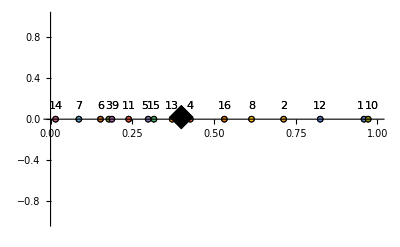

```mathematica
Show[ListPlot[Table[{{alphas[[i]],0}},{i,m}],Axes->{True,False},AxesStyle->Thick,Ticks->Range[0,1,.1],PlotMarkers->marker,PlotRange->{{0,1},Automatic},TicksStyle->Directive[Black, 12]],ListPlot[{{s[[1]]*e/Total[s],0.02}},PlotStyle->Black,PlotMarkers->{"◆",25}],labels,Method->{"AxesInFront"->False}]
```

```mathematica
Export["figS6_S7_strategies_"<>oligoStatus<>".svg",%];
```

## continuous space

```mathematica
If[oligoStatus=="oligo",
thisName="B";,
thisName="D";]
```

```mathematica
nInit=ConstantArray[1/m,m]*l;
```

```mathematica
continuousSol=NDSolveValue[{n'[t]==dnContinuous[n[t]],n[0]==nInit},n,{t,0,steps}];
```

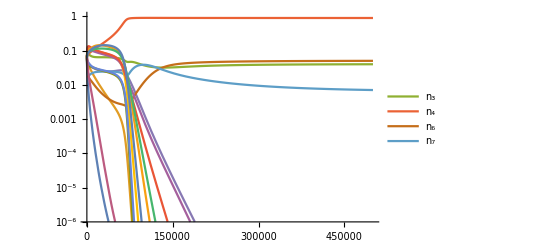

```mathematica
thisPlot=plotTimeseries[continuousSol]
```

```mathematica
Export["figS6"<>thisName<>"_left_timeSeries_continuous.svg",thisPlot];
```

## lattice model

```mathematica
(*linear*)
coordinatesLinear=makeLinearSpace[m];
spatialStructureLinear=getSpatialStructure[coordinatesLinear,linearBasis,m];
```

```mathematica
(*square*)
coordinatesSquare=makeSquareSpace[m];
spatialStructureSquare=getSpatialStructure[coordinatesSquare,squareBasis,Sqrt[m]];
```

```mathematica
(*hexagonal*)
coordinatesHexagonal=makeHexagonalSpace[m];
spatialStructureHexagonal=getHexagonalStructure[coordinatesHexagonal,hexagonalBasis];
```

```mathematica
coordinates={coordinatesLinear,coordinatesSquare,coordinatesHexagonal};
latticeStructures={spatialStructureLinear,spatialStructureSquare,spatialStructureHexagonal};
latticeNames={"linear","square","hexagonal"};
```

```mathematica
timeSeriesPlots={0,0,0};
spatialStratPlots={0,0,0};
spatialSurvivalPlots={0,0,0};
```

```mathematica
For[index=1,index≤Length[latticeStructures],++index,

thisName="seed"<>ToString[seed]<>"_m"<>ToString[m]<>"_"<>latticeNames[[index]]<>"_"<>oligoStatus;
thisStructure=latticeStructures[[index]];
theseCoords=coordinates[[index]];

v=getNeighborVectors[thisStructure];
z=Length[v[[1]]];

thisSol=NDSolveValue[{n'[t]==dn[n[t]],n[0]==nInit},n,{t,0,.6*steps}];
timeSeriesPlots[[index]]=plotTimeseries[thisSol];

nFinal=thisSol[thisSol["Domain"][[1,2]]];

(*spatial plotting*)
boundaries={{Min[theseCoords[[;;,1]]]-0.5,Max[theseCoords[[;;,1]]]+0.5},{Min[theseCoords[[;;,2]]]-0.5,Max[theseCoords[[;;,2]]]+0.5}};
scale={boundaries[[1,2]]-boundaries[[1,1]],boundaries[[2,2]]-boundaries[[2,1]]};
labelMarkers=Table[{i,Medium},{i,m}];
stratLabels=ListPlot[Table[{thisStructure[[i,1]]+{0,-scale[[2]]/60}(*+{scale[[1]]/90,scale[[2]]/30}*)},{i,m}],PlotMarkers->labelMarkers,PlotStyle->White];


spatialStratPlots[[index]]=Show[ListPlot[Table[{theseCoords[[i]]},{i,m}],PlotStyle->colors,PlotMarkers->{{"●",Scaled[.125]}},PlotRange->boundaries,Axes->False]//Quiet,stratLabels];

(*spatial survival plotting*)
cutoff=10^-7;
extinctIndices={};


For[index2=1,index2≤m,index2++,
If[nFinal[[index2]]<cutoff,extinctIndices=Join[extinctIndices,{index2}];];
];

survivalColors=Table[If[MemberQ[extinctIndices,i],Gray,colors[[i]]],{i,m}];


spatialSurvivalPlots[[index]]=Show[ListPlot[Table[{theseCoords[[i]]},{i,m}],PlotStyle->survivalColors,PlotMarkers->{{"●",Scaled[.125]}},PlotRange->boundaries,Axes->False]//Quiet,stratLabels];


];
```

```mathematica
If[oligoStatus=="oligo",
Export["figS6B_right_timeseries_lattice.svg",timeSeriesPlots[[1]]];

Export["figS7A_left_square.svg",spatialSurvivalPlots[[2]]];
Export["figS7A_right_hexagonal.svg",spatialSurvivalPlots[[3]]];

,
Export["figS6D_right_timeseries_lattice.svg",timeSeriesPlots[[1]]];

Export["figS7C_left_square.svg",spatialSurvivalPlots[[2]]];
Export["figS7C_right_hexagonal.svg",spatialSurvivalPlots[[3]]];

]
```

## Effective number of species (only for oligotroph case)

```mathematica
effectiveSpecies[n_]:=
Module[{},
modN=n/.{x_/;x<0->0};
entropyTable=Table[-modN[[i]]*Log[modN[[i]]],{i,Length[modN]}]//Quiet;
entropyTable2=entropyTable/.{Indeterminate->0};
entropy=entropyTable2//Total;
mEff=E^entropy
]
```

```mathematica
mData={0,0,0};
xDims={16,2,2};
```

```mathematica
lSeries={.1,1,Sqrt[10],7,10,15,20,30};
```

```mathematica
For[i=1,i≤Length[latticeStructures],++i,

mSeries=ConstantArray[0,Length[lSeries]];

For[j=1,j≤Length[lSeries],++j,


thisL=lSeries[[j]];
thisnInit=ConstantArray[1/m,m]*thisL;

thisStructure=latticeStructures[[i]];
theseCoords=coordinates[[i]];

v=getNeighborVectors[thisStructure];
z=Length[v[[1]]];

thisSol=NDSolveValue[{n'[t]==dn[n[t]],n[0]==thisnInit},n,{t,0,steps}];
nFinal=thisSol[thisSol["Domain"][[1,2]]];


mSeries[[j]]=effectiveSpecies[nFinal/thisL];
];
mData[[i]]=mSeries;
];
```

```mathematica
mPlots={0,0,0};
```

```mathematica
latticeIndex=1;
mPlots[[latticeIndex]]=ListLogLinearPlot[Transpose[{lSeries*16,mData[[latticeIndex]]}],TicksStyle->Black,PlotStyle->Directive[PointSize[.015]],Ticks->{{.01,.1,1,10,100,1000,10000},Range[1,2,.2]},PlotRange->{{.8,1000},{1,1.8}},LabelStyle->{FontSize->12},Joined->True,PlotMarkers->Automatic]
```

```mathematica
latticeIndex=2;
mPlots[[latticeIndex]]=ListLogLinearPlot[Transpose[{lSeries,mData[[latticeIndex]]}],TicksStyle->Black,PlotStyle->Directive[PointSize[.015]],Ticks->{{.01,.1,1,10,100,1000,10000},Range[1,2,.2]},PlotRange->{{.06,100},{1,1.8}},LabelStyle->{FontSize->12},Joined->True,PlotMarkers->Automatic]
```

```mathematica
latticeIndex=3;
mPlots[[latticeIndex]]=ListLogLinearPlot[Transpose[{lSeries,mData[[latticeIndex]]}],TicksStyle->Black,PlotStyle->Directive[PointSize[.015]],Ticks->{{.01,.1,1,10,100,1000,10000},Range[1,2,.2]},PlotRange->{{.06,100},{1,1.8}},LabelStyle->{FontSize->12},Joined->True,PlotMarkers->Automatic]
```

```mathematica
If[oligoStatus=="oligo",
Export["figS6C_right_effectiveSpecies_latticeLinear.svg",mPlots[[1]]];
Export["figS7B_left_effectiveSpecies_square.svg",mPlots[[2]]];
Export["figS7B_right_effectiveSpecies_hexagonal.svg",mPlots[[3]]];
]
```

```mathematica
(*continuous*)
lContinuousSteps=10^7;
mContinuous=ConstantArray[0,Length[lSeries]];
For[j=1,j≤Length[lSeries]-1,++j,


thisL=lSeries[[j]];
thisnInit=ConstantArray[1/m,m]*thisL;


thisSol=NDSolveValue[{n'[t]==dnContinuous[n[t]],n[0]==thisnInit},n,{t,0,lContinuousSteps},Method->{"EventLocator","Event"->Norm[n'[t]]<10^-13}];
nFinal=thisSol[thisSol["Domain"][[1,2]]];


mContinuous[[j]]=effectiveSpecies[nFinal/thisL];
];
```

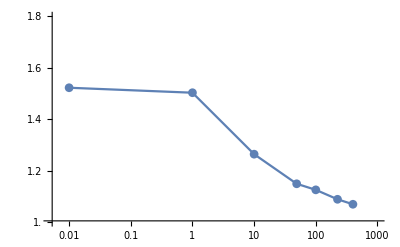

```mathematica
ListLogLinearPlot[Transpose[{lSeries[[1;;-2]]^2,mContinuous[[1;;-2]]}],TicksStyle->Black,PlotStyle->Directive[PointSize[.015]],Ticks->{{.01,.1,1,10,100,1000,10000},Range[1,2,.2]},PlotRange->{{.005,1000},{1,1.8}},LabelStyle->{FontSize->12},Joined->True,PlotMarkers->Automatic]
```

```mathematica
If[oligoStatus=="oligo",
Export["figS6C_left_effectiveSpecies_continuous.svg",%];]
```